```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis/UP_sample/EXTRA_UPSAMPLE"];
meamFiles={"TI_EpotminusEperf_all2_EXTRA_AGAIN","TI_EpotminusEperf_all_EXTRA_AGAIN"};
dftUPFiles={"TI_UP_E0all_EXTRA_AGAIN","TI_UP_Fall_EXTRA_AGAIN"};
meamData=Table[ReadList[meamFiles[[i]],{Number, Number,Number,Number,Number,Number,Number,Number,Number}],{i,1,2}];
dftUPData=Table[ReadList[dftUPFiles[[i]],{Number}],{i,1,2}];
temps={300,760,1900,2500,3200,3805};
lambda=Table[i/10,{i,0,10}]//N;
vols={4.685,4.730,4.759,4.801,4.850};
eVcel2meVatom=1000/64;
```

```mathematica
meamData[[1]][[1]]
```

{7501,7501.,3901.7,3800.8,391.25,405.51,-14.25,-23.16,-23.19}

```mathematica
meam=Partition[Transpose[meamData[[2]]][[5]],191];
dft=eVcel2meVatom*Table[Partition[Transpose[dftUPData[[1]]][[1]],191][[i]]-Partition[Transpose[dftUPData[[1]]][[1]],191][[i]][[1]],{i,1,5}];
dftf=eVcel2meVatom*Table[Partition[Transpose[dftUPData[[2]]][[1]],191][[i]]-Partition[Transpose[dftUPData[[2]]][[1]],191][[i]][[1]],{i,1,5}];
```

```mathematica
(*Energy MVT TI UP-sample*)
GraphicsGrid[{{ListLinePlot[Table[(dft-meam)[[i]],{i,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\nUP-samples","UP-sample (meV/atom)"},ImageSize->600],ListPlot[Table[Table[Mean[(dft-meam)[[j]][[1;;i]]],{i,1,191}],{j,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\nUP-samples","UP-sample mean\n (meV/atom)"},ImageSize->600],ListPlot[Table[Table[StandardDeviation[(dft-meam)[[j]][[1;;i]]/Sqrt[i]],{i,2,191}],{j,1,5}],PlotLegends->SwatchLegend[vols],AxesLabel->{"Number of\n UP-samples","UP-sample uncertainty\n (meV/atom)"},PlotRange->All,ImageSize->600]}},ImageSize->2050]
Table[{Mean[(dft-meam)[[i]]],StandardDeviation[(dft-meam)[[i]]],StandardDeviation[(dft-meam)[[i]]]/Sqrt[Length[(dft-meam)[[i]]]]},{i,1,5}]//TableForm
```

-Graphics-

17.2815 | 6.0877 | 0.44049
8.50648 | 4.79329 | 0.34683
4.1014 | 4.89907 | 0.354484
-1.57761 | 4.41958 | 0.319789
-6.0171 | 5.11094 | 0.369815

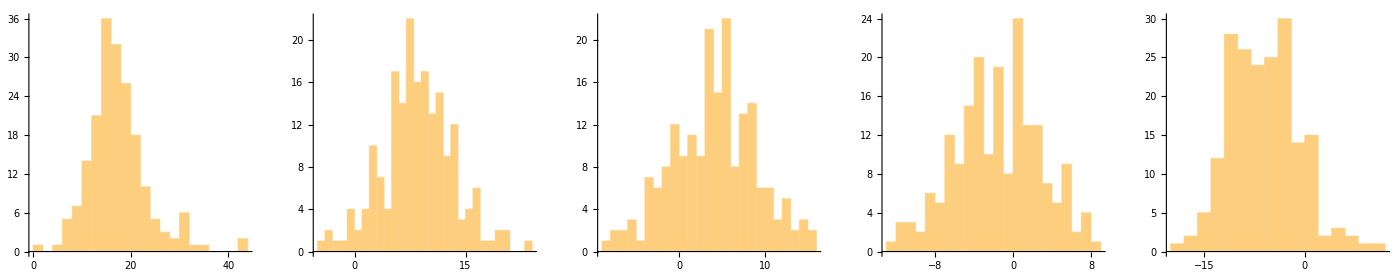

```mathematica
GraphicsGrid[{Table[Histogram[(dft-meam)[[i]],20],{i,1,5}]},ImageSize->1400]
```

```mathematica
edist=Table[EstimatedDistribution[(dft-meam)[[i]],NormalDistribution[μ,σ]],{i,1,5}];
edistf=Table[EstimatedDistribution[(dftf-meam)[[i]],NormalDistribution[μ,σ]],{i,1,5}];
edist//TableForm
edistf//TableForm
```

NormalDistribution[507.742,61.2466]
NormalDistribution[494.324,63.303]
NormalDistribution[498.355,63.227]
NormalDistribution[468.38,64.0701]
NormalDistribution[457.78,60.9779]

NormalDistribution[496.226,59.8661]
NormalDistribution[482.468,61.9017]
NormalDistribution[486.279,61.7772]
NormalDistribution[456.347,62.5579]
NormalDistribution[445.071,59.4952]

```mathematica
Table[Mean[(dft-meam)[[i]]],{i,1,5}]
Table[Mean[(dftf-meam)[[i]]],{i,1,5}]
```

{17.2815,8.50648,4.1014,-1.57761,-6.0171}

{5.76573,-3.3491,-7.97472,-13.6102,-18.7258}

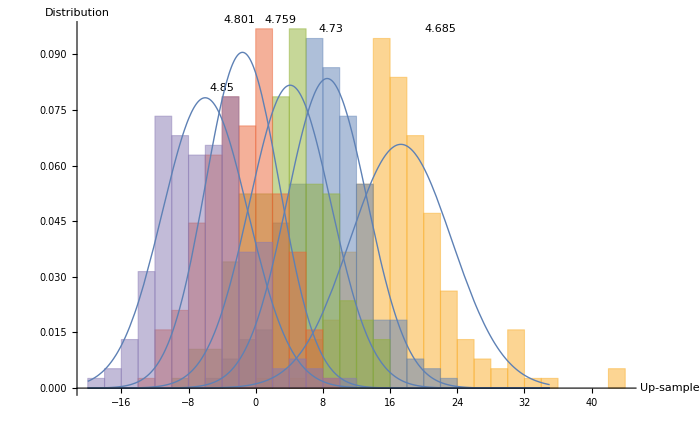

```mathematica
ldata=Table[Labeled[(dft-meam)[[i]],vols[[i]],Above],{i,1,5}];
Show[Histogram[ldata,20,"PDF",AxesLabel->{"Up-sample","Distribution"}],Plot[Table[PDF[edist[[i]],x],{i,1,5}],{x,-20,35},PlotStyle->Thick],ImageSize->700]
```

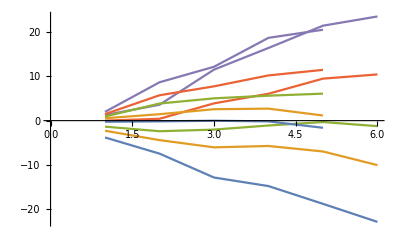

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];
andyFah=Partition[Transpose[ReadList["Fah_surface_andy_tu-tild",{Number,Number,Number,Number}]][[3]],5];
MVTintAll=Transpose@ReadList["MVT_intall",{Number, Number,Number,Number,Number}];
Show[ListPlot[MVTintAll,Joined->True],ListPlot[andyFah,Joined->True]]
```

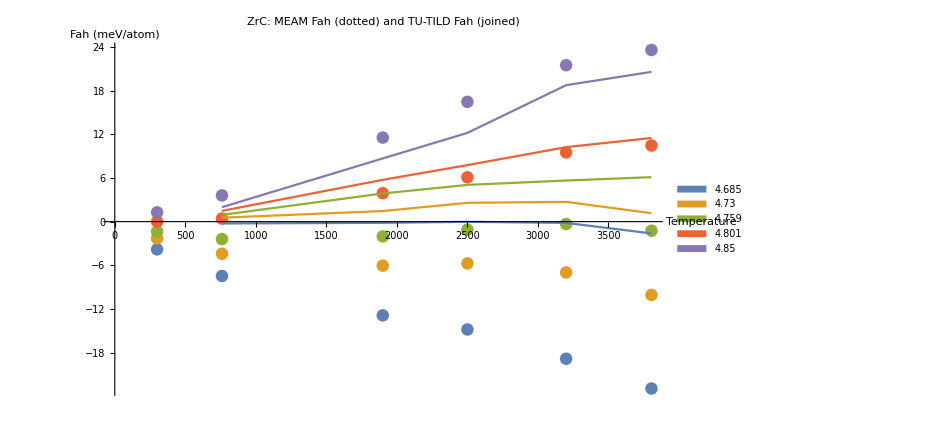

```mathematica
MVTtemps=Table[Transpose[{temps,MVTintAll[[i]]}],{i,1,5}];
andyFahtemps=Table[Transpose[{DeleteCases[temps,300],andyFah[[i]]}],{i,1,5}];
Show[ListPlot[MVTtemps,PlotLegends->SwatchLegend[vols]],ListLinePlot[andyFahtemps],AxesLabel->{"Temperature","Fah (meV/atom)"},PlotLabel->"ZrC: MEAM Fah (dotted) and TU-TILD Fah (joined)",ImageSize->700]
```

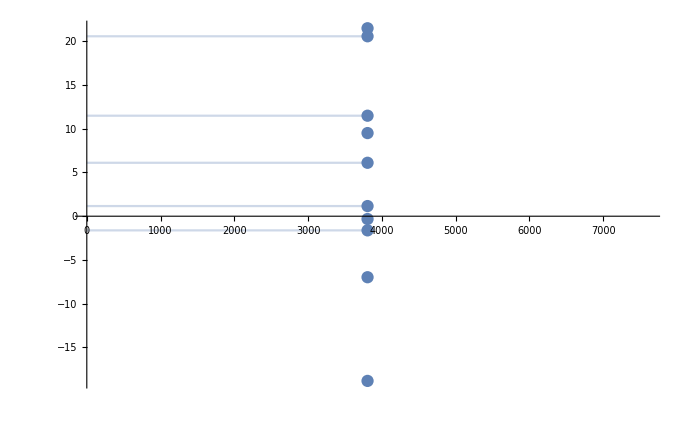

```mathematica
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{axisOrigin,#2},{#1,#2}}&@@@a]};
Show[ListPlot[Transpose@{Table[3805,{i,1,5}],Transpose[MVTintAll][[5]]}],horizontalListPlotFill@ListPlot[Transpose@{Table[3805,{i,1,5}],Transpose[andyFah][[5]]}]]
```

```mathematica
Transpose[andyFah][[5]]
Transpose[MVTintAll][[5]]
Table[Mean[(dft-meam)[[i]]],{i,1,5}]
Transpose[MVTintAll][[5]]+Table[Mean[(dft-meam)[[i]]],{i,1,5}]
```

{-1.61955,1.16037,6.11159,11.4963,20.5815}

{-18.84,-6.98,-0.32,9.51,21.5}

{17.2815,8.50648,4.1014,-1.57761,-6.0171}

{-1.55849,1.52648,3.7814,7.93239,15.4829}

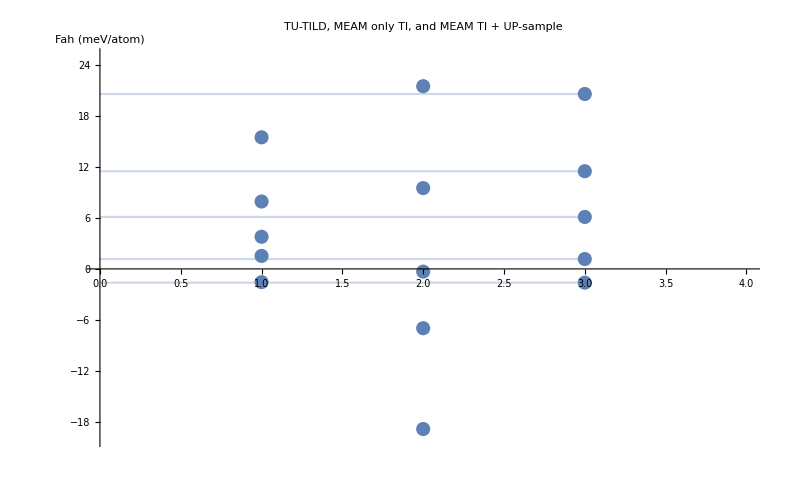

```mathematica
Show[horizontalListPlotFill@ListPlot[Transpose@{Table[3,{i,1,5}],Transpose[andyFah][[5]]},PlotRange->{{0,4},{-20,25}},PlotLabel->"TU-TILD, MEAM only TI, and MEAM TI + UP-sample",AxesLabel->{"","Fah (meV/atom)"}],ListPlot[Transpose@{Table[2,{i,1,5}],Transpose[MVTintAll][[5]]}],ListPlot[Transpose@{Table[1,{i,1,5}],Transpose[MVTintAll][[5]]+Table[Mean[(dft-meam)[[i]]],{i,1,5}]}]]
```

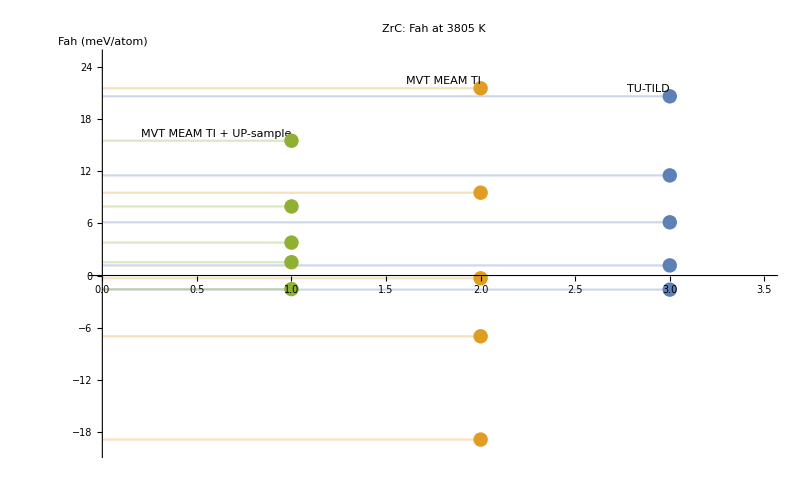

```mathematica
horizontalListPlotFill@ListPlot[{Labeled[Transpose@{Table[3,{i,1,5}],Transpose[andyFah][[5]]},"TU-TILD",Above],Labeled[Transpose@{Table[2,{i,1,5}],Transpose[MVTintAll][[5]]},"MVT MEAM TI",Above],Labeled[Transpose@{Table[1,{i,1,5}],Transpose[MVTintAll][[5]]+Table[Mean[(dft-meam)[[i]]],{i,1,5}]},"MVT MEAM TI + UP-sample",Above]},PlotLegends->SwatchLegend["TU-TILD","MVT MEAM TI","MVT MEAM TI + UPsample"],PlotRange->{{0,3.5},{-20,25}},PlotLabel->"ZrC: Fah at 3805 K",AxesLabel->{"","Fah (meV/atom)"},Ticks->{None,Automatic}]
```